# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

H:\My Drive\Doctorado\Quinto semestre\RESEARCH\Codes

```mathematica
Get["QMB.wl"]
```

```mathematica
?IsingNNOpenHamiltonian
```

```mathematica
?DensityMatrix
```

```mathematica
?StateEvolution
```

```mathematica
?Dyad
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Choi & Kraus operators

## Setting parameters and global variables

```mathematica
{hx,hz,J,L}={1.,1./2,{1.,1.},3}
```

{1.,0.5,{1.,1.},3}

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Chop[Eigensystem[H]];
```

```mathematica
U[t_]:=MatrixExp[-I H t];
```

```mathematica
SeedRandom[32371];
(*Estado inicial de los qubits en el entorno Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
ψ0E=RandomChainProductState[L-1]
```

{0.527379+0. ⅈ,-0.599935-0.514447 ⅈ,-0.0473727+0.166532 ⅈ,0.216339-0.143232 ⅈ}

```mathematica
(*Estado inicial 0⊗Subscript[ψ, 0E]*)
ψ0SE=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{0}],ψ0E]
```

{0.527379+0. ⅈ,-0.599935-0.514447 ⅈ,-0.0473727+0.166532 ⅈ,0.216339-0.143232 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Dyad[ψ0SE]
```

{{0.278128+0. ⅈ,-0.316393+0.271308 ⅈ,-0.0249834-0.0878254 ⅈ,0.114092+0.0755376 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.316393-0.271308 ⅈ,0.624577+0. ⅈ,-0.0572513+0.124279 ⅈ,-0.0561038-0.197225 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.0249834+0.0878254 ⅈ,-0.0572513-0.124279 ⅈ,0.0299771+0. ⅈ,-0.0341013+0.029242 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.114092-0.0755376 ⅈ,-0.0561038+0.197225 ⅈ,-0.0341013-0.029242 ⅈ,0.0673179+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
t=50.;
```

```mathematica
(*Compute Subscript[ρ, 1](t) = Subscript[Tr, E](Ui⊗ψ0Ej⊗ψ0E U^†) *)
MatrixForm[superOperator=
Transpose[
Flatten[
Table[
ρfSE=Dyad[
StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i}],ψ0E],eigVals,eigVecs],
StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j}],ψ0E],eigVals,eigVecs]
];
Flatten[MatrixPartialTrace[ρfSE,Range[2,L],2]],
{i,0,1},{j,0,1}
],
1]
]]
```

(0.521038+0. ⅈ | 0.0427558+0.16995 ⅈ | 0.0427558-0.16995 ⅈ | 0.30763+0. ⅈ
-0.0447521-0.188054 ⅈ | -0.277838+0.364094 ⅈ | -0.15604-0.0170876 ⅈ | 0.00548597-0.0696096 ⅈ
-0.0447521+0.188054 ⅈ | -0.15604+0.0170876 ⅈ | -0.277838-0.364094 ⅈ | 0.00548597+0.0696096 ⅈ
0.478962+0. ⅈ | -0.0427558-0.16995 ⅈ | -0.0427558+0.16995 ⅈ | 0.69237+0. ⅈ)

```mathematica
superOperator.{1,0,0,0}
```

{0.521038+0. ⅈ,-0.0447521-0.188054 ⅈ,-0.0447521+0.188054 ⅈ,0.478962+0. ⅈ}

```mathematica
Chop[superOperator//Eigensystem]
```

{{1.,-0.320401-0.345273 ⅈ,-0.320401+0.345273 ⅈ,0.298535},{{0.601093,0.0219309-0.141943 ⅈ,0.0219309+0.141943 ⅈ,0.772936},{0.0401231+0.259442 ⅈ,0.0564994-0.157054 ⅈ,0.913401,-0.0401231-0.259442 ⅈ},{0.0401231-0.259442 ⅈ,0.913401,0.0564994+0.157054 ⅈ,-0.0401231+0.259442 ⅈ},{-0.687123,-0.0375185+0.162649 ⅈ,-0.0375185-0.162649 ⅈ,0.687123}}}

```mathematica
MatrixForm[CJmatrix=Reshuffle[superOperator]]
```

(0.521038+0. ⅈ | 0.0427558+0.16995 ⅈ | -0.0447521-0.188054 ⅈ | -0.277838+0.364094 ⅈ
0.0427558-0.16995 ⅈ | 0.30763+0. ⅈ | -0.15604-0.0170876 ⅈ | 0.00548597-0.0696096 ⅈ
-0.0447521+0.188054 ⅈ | -0.15604+0.0170876 ⅈ | 0.478962+0. ⅈ | -0.0427558-0.16995 ⅈ
-0.277838-0.364094 ⅈ | 0.00548597+0.0696096 ⅈ | -0.0427558+0.16995 ⅈ | 0.69237+0. ⅈ)

```mathematica
CJmatrix//Eigensystem
```

{{1.18379,0.529173,0.262796,0.0242444},{{-0.386308+0.479065 ⅈ,0.10242+0.104058 ⅈ,-0.170038-0.319199 ⅈ,0.684941+0. ⅈ},{0.111055+0.00718255 ⅈ,-0.265526-0.549981 ⅈ,0.475409+0.394461 ⅈ,0.48272+0. ⅈ},{-0.0485187+0.461546 ⅈ,0.283434+0.463159 ⅈ,0.600103+0.320165 ⅈ,-0.164746+0. ⅈ},{-0.390165+0.491194 ⅈ,-0.20127-0.519941 ⅈ,0.0272137-0.155615 ⅈ,-0.520284+0. ⅈ}}}

```mathematica
MatrixForm/@{#,Reshuffle[#]}&[Table[m[i,j],{i,4},{j,4}]]
```

{(m[1,1] | m[1,2] | m[1,3] | m[1,4]
m[2,1] | m[2,2] | m[2,3] | m[2,4]
m[3,1] | m[3,2] | m[3,3] | m[3,4]
m[4,1] | m[4,2] | m[4,3] | m[4,4]),(m[1,1] | m[1,2] | m[2,1] | m[2,2]
m[1,3] | m[1,4] | m[2,3] | m[2,4]
m[3,1] | m[3,2] | m[4,1] | m[4,2]
m[3,3] | m[3,4] | m[4,3] | m[4,4])}

```mathematica
KrausOperators=Table[SparseArray[FromDigits[{r,#1,#2},2]+1->1,8].U[t=1].SparseArray[FromDigits[{s,0,0},2]+1->1,8],{r,0,1},{s,0,1}]&@@@Tuples[{0,1},2]
```

{{{0.147987+0.358403 ⅈ,0.191468-0.286941 ⅈ},{0.191468-0.286941 ⅈ,0.133578-0.149483 ⅈ}},{{0.191468-0.286941 ⅈ,-0.303873+0.25267 ⅈ},{-0.333272+0.255453 ⅈ,-0.453064-0.0176966 ⅈ}},{{-0.131625+0.0739518 ⅈ,-0.168937+0.294765 ⅈ},{-0.345416+0.0710369 ⅈ,0.0334327-0.374144 ⅈ}},{{-0.345416+0.0710369 ⅈ,0.0334327+0.430163 ⅈ},{-0.281707+0.290624 ⅈ,-0.0627265-0.180099 ⅈ}}}

```mathematica
Chop@Sum[ConjugateTranspose[K].K,{K,KrausOperators}]
```

{{1.,0},{0,1.}}

```mathematica
ρ={1,x,y,z}.(Pauli/@Range[0,3])/2
```

{{(1+z)/2,1/2 (x-ⅈ y)},{1/2 (x+ⅈ y),(1-z)/2}}

```mathematica
ρFinal=Chop[FullSimplify[Total[#.ρ.ConjugateTranspose[#]&/@KrausOperators]]]
```

{{0.49663-0.142145 x+0.327167 y-0.0801301 z,(-0.0183884+0.00905543 ⅈ)+(0.170515-0.0686733 ⅈ) x+(0.158621+0.309188 ⅈ) y-(0.0245583-0.21293 ⅈ) z},{(-0.0183884-0.00905543 ⅈ)+(0.170515+0.0686733 ⅈ) x+(0.158621-0.309188 ⅈ) y-(0.0245583+0.21293 ⅈ) z,0.50337+0.142145 x-0.327167 y+0.0801301 z}}

```mathematica
BlochVectorFinal=Chop[FullSimplify[Tr[#.ρFinal]]]&/@(Pauli/@Range[0,3])[[2;;]]
```

{-0.0367768+0.34103 x+0.317242 y-0.0491167 z,-0.0181109+0.137347 x-0.618376 y-0.425859 z,-0.00674017-0.28429 x+0.654333 y-0.16026 z}

```mathematica
(BlochVectorFinal/.{x->#1,y->#2,z->#3})&@@{0,0,0}
```

{-0.0367768,-0.0181109,-0.00674017}

```mathematica
SeedRandom[23049];
ListPointPlot3D[(BlochVectorFinal/.{x->#1,y->#2,z->#3})&@@@RandomPoint[Sphere[{1,0,0},0.01],1000],Axes->True,PlotTheme->"Detailed",BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
RandomPoints=Table[{θ,ϕ}={RandomReal[{0,Pi/16}],RandomReal[{0,2Pi}]};
{Cos[ϕ]Sin[θ],Sin[θ]Sin[ϕ],Cos[θ]},100];
```

```mathematica
sphere=Graphics3D[{{Opacity[0.5],Sphere[]},Point[RandomPoints]},Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
Show[sphere,ListPointPlot3D[(BlochVectorFinal/.{x->#1,y->#2,z->#3})&@@@RandomPoints,Axes->True,PlotTheme->"Detailed"]]
```

-Graphics3D-

# Evolution of Choi eigenvalues

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
```

```mathematica
(*caothic*)
{hx,hz,J,L}={1.,0.5,1,4};
```

```mathematica
(*Regular*)
{hx,hz,J,L}={1.,3.0,1,5};
```

```mathematica
Clear[H];
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
Clear[U];
U[t_]:=MatrixExp[-I H t];
SeedRandom[32372];
(*Estado inicial de los qubits en el entorno Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
ψ0E=RandomChainProductState[L-1];
(*Estado inicial 0⊗Subscript[ψ, 0E]*)
ψ0SE=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{0}],ψ0E];
```

```mathematica
(*Compute Subscript[ρ, 1](t) = Subscript[Tr, E](Ui⊗ψ0Ej⊗ψ0E U^†) *)
```

```mathematica
tlist=Range[0,1,0.01];
superoperators={};
Do[
superOperator=
Transpose[Flatten[Table[ρfSE=Dyad[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i}],ψ0E],eigenval,eigenvec],
StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j}],ψ0E],eigenval,eigenvec]];Flatten[MatrixPartialTrace[ρfSE,Range[2,L],2]],{i,0,1},{j,0,1}],1]];
AppendTo[superoperators,superOperator];
,{t,tlist}];
supereigen=Table[Eigensystem[i],{i,superoperators}];
rhos=Table[Chop[rho[supereigen[[i]][[2]][[1]]]],{i,Length[tlist]}];
stablepoints=Table[bloch[i],{i,rhos}];
```

```mathematica
points=Table[Show[ListPointPlot3D[{stablepoints[[i]]},BoxRatios->{1, 1, 1},PlotRange->{{-1,1},{-1,1},{-1,1}},AxesLabel->{Style["x",25,Black],Style["y",25,Black],Style["z",25,Black]}],plotsphere2],{i,Length[tlist]}];
```

```mathematica
ListAnimate[points,AnimationRunning->False]
```

```mathematica
plots=Table[ComplexListPlot[Chop[supereigen[[i]][[1]]],PlotLabel->Style["t = "<>ToString[tlist[[i]]],30,Black],PlotRange->{{-1.2,1.2},{-1.2,1.2}},AspectRatio->1],{i,Length[tlist]}];
```

```mathematica
(*regular*)
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
(*chaotic*)
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
Export["supereigenvalues_regular.gif",plots,"DisplayDurations"->0.5]
```

supereigenvalues_regular.gif

```mathematica
CJmatrixs=Table[Reshuffle[i],{i,superoperators}];
choieigenvals=Table[Eigenvalues[i],{i,CJmatrixs}];
```

```mathematica
MatrixForm[ArrayReshape[#,{2,2}]]&/@Eigenvectors[CJmatrixs[[2]]]
```

{(0.646733-0.277163 ⅈ | -0.0140657-0.0686967 ⅈ
-0.0141264-0.0686837 ⅈ | 0.703621+0. ⅈ),(-0.649851+0.278666 ⅈ | 0.00538671-0.0117117 ⅈ
-0.00723675+0.010307 ⅈ | 0.706904+0. ⅈ),(0.0090451+0.00249861 ⅈ | 0.44295-0.557834 ⅈ
-0.520558+0.470365 ⅈ | -0.0174744+0. ⅈ),(0.0640943-0.027561 ⅈ | 0.197606+0.669691 ⅈ
0.085146+0.703882 ⅈ | 0.0699841+0. ⅈ)}

```mathematica
MatrixForm[ArrayReshape[#,{2,2}]]&/@Eigenvectors[CJmatrixs[[2]]]
```

{(-0.700315-0.0676619 ⅈ | -0.00342455+0.070491 ⅈ
-0.00337794+0.0704925 ⅈ | -0.703576+0. ⅈ),(-0.70392-0.0667253 ⅈ | 0.00435833-0.00705816 ⅈ
-0.0169925+0.00442771 ⅈ | 0.706871+0. ⅈ),(-0.00546152-0.00544494 ⅈ | -0.643798+0.293563 ⅈ
0.68637-0.166853 ⅈ | 0.0184928+0. ⅈ),(0.0703013-0.00479928 ⅈ | 0.0909851+0.697149 ⅈ
-0.0433699+0.702771 ⅈ | 0.0705103+0. ⅈ)}

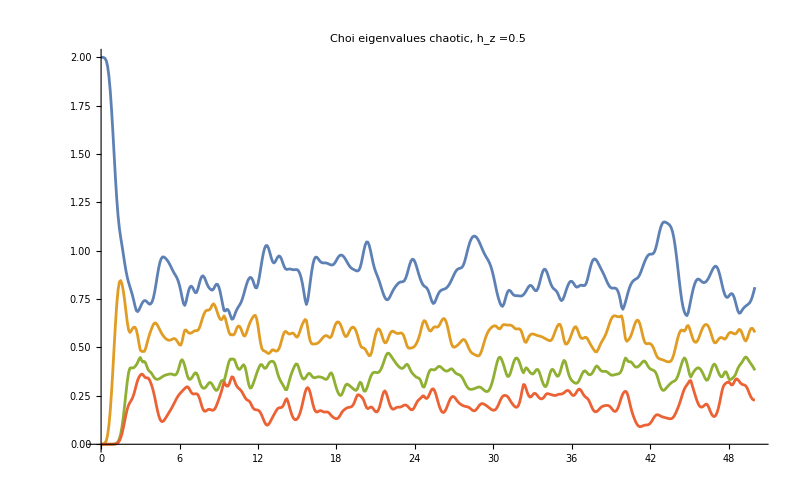

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues chaotic, h_z ="<>ToString[hz],30,Black]]
```

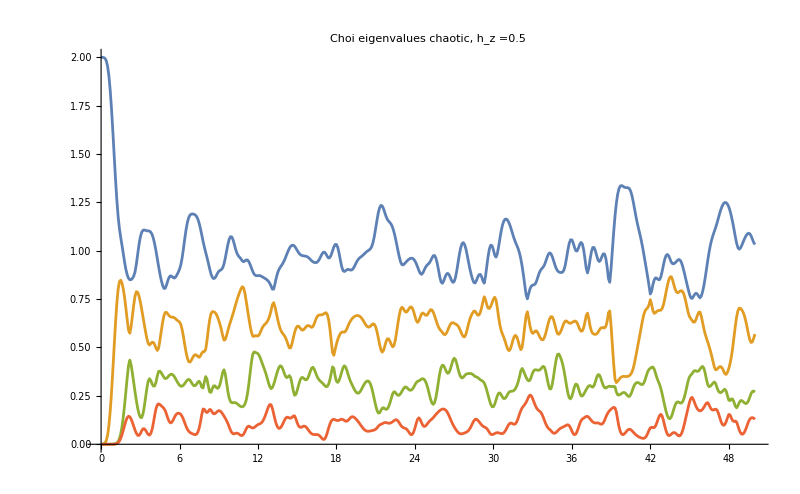

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues chaotic, h_z ="<>ToString[hz],30,Black]]
```

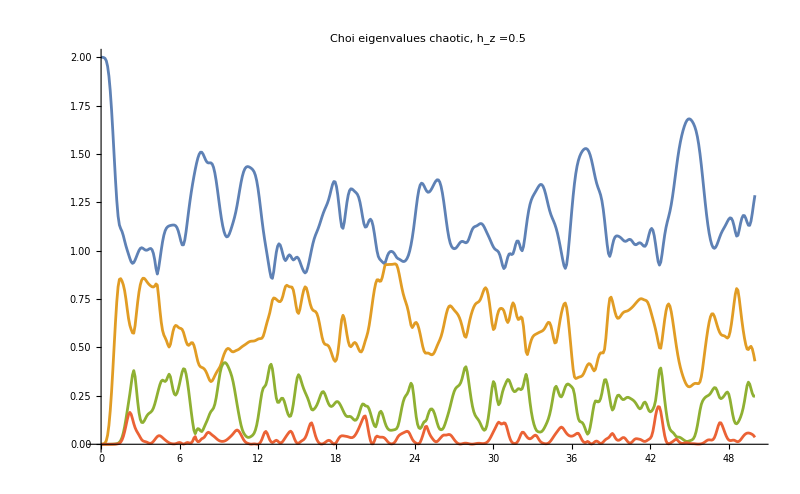

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues chaotic, h_z ="<>ToString[hz],30,Black]]
```

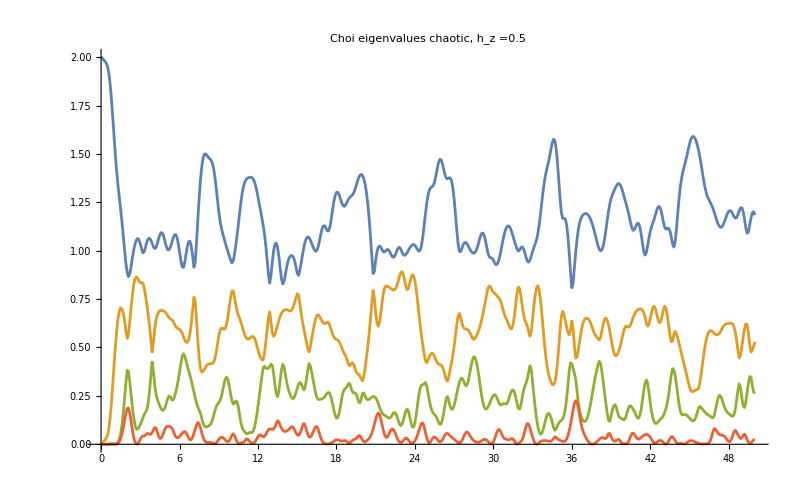

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues chaotic, h_z ="<>ToString[hz],30,Black]]
```

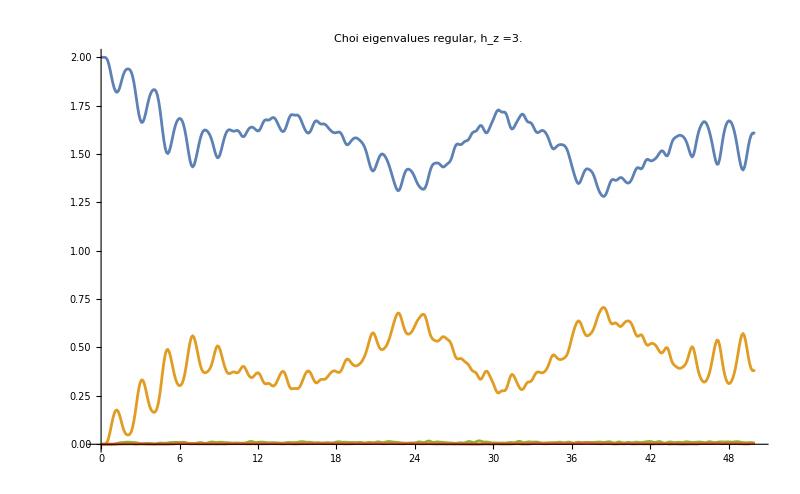

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues regular, h_z ="<>ToString[hz],30,Black]]
```

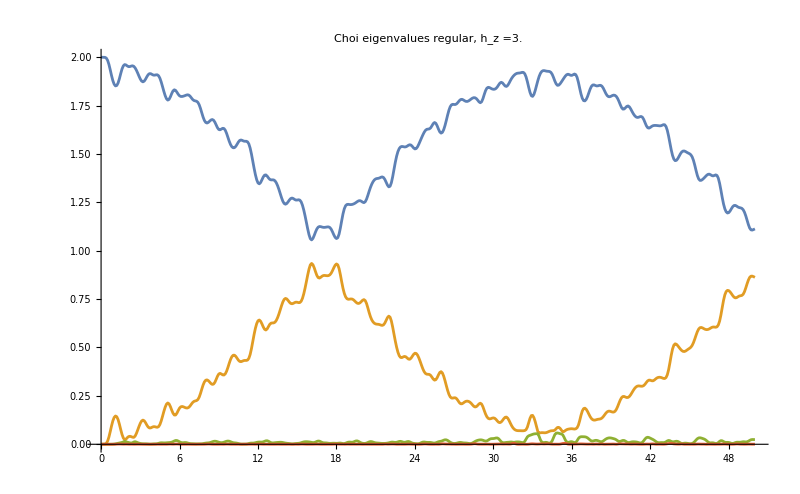

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues regular, h_z ="<>ToString[hz],30,Black]]
```

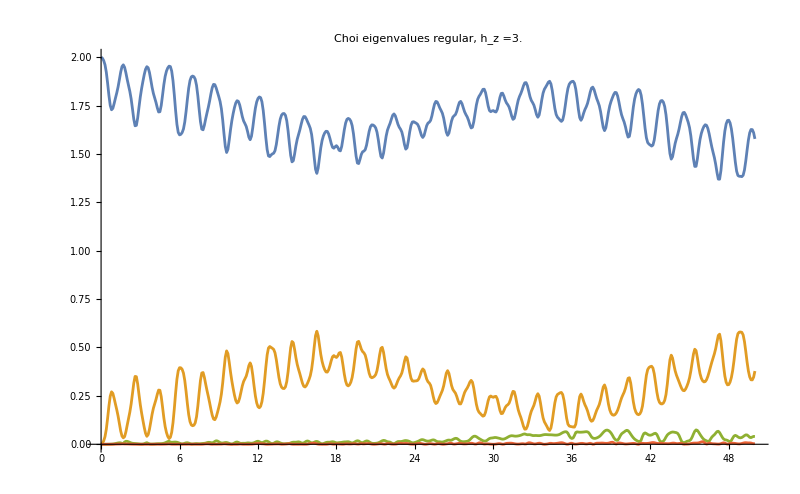

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues regular, h_z ="<>ToString[hz],30,Black]]
```

```mathematica
choieigenvals[[1;;5]]//MatrixForm
```

(2. | -1.66533×10^-16 | 0. | 0.
1.99936 | 0.000642104 | 3.05177×10^-9 | 9.95081×10^-13
1.99916 | 0.000841538 | 1.52068×10^-6 | 6.77277×10^-10
1.99899 | 0.000972025 | 0.0000418533 | 2.30819×10^-8
1.99512 | 0.00480767 | 0.0000712238 | 2.2337×10^-7)

```mathematica
CJmatrixs=Table[Reshuffle[i],{i,superoperators}];
```

```mathematica
choisystem=Table[Transpose[Sort[Transpose[Eigensystem[i]]]],{i,CJmatrixs}];
```

```mathematica
choisystem[[1]]//Chop
```

{{0,0,0,2.},{{0,0,-1.,0},{0,1.,0,0},{-0.707107,0,0,0.707107},{0.707107,0,0,0.707107}}}

```mathematica
choisystem[[2]]//Chop
```

{{0,3.05177×10^-9,0.000642104,1.99936},{{0.0640943-0.027561 ⅈ,0.197606+0.669691 ⅈ,0.085146+0.703882 ⅈ,0.0699841},{0.0090451+0.00249861 ⅈ,0.44295-0.557834 ⅈ,-0.520558+0.470365 ⅈ,-0.0174744},{-0.649851+0.278666 ⅈ,0.00538671-0.0117117 ⅈ,-0.00723675+0.010307 ⅈ,0.706904},{0.646733-0.277163 ⅈ,-0.0140657-0.0686967 ⅈ,-0.0141264-0.0686837 ⅈ,0.703621}}}

## Trajectory of the stationary point - Regular

```mathematica
(*Compute Subscript[ρ, 1](t) = Subscript[Tr, E](Ui⊗ψ0Ej⊗ψ0E U^†) *)
tlist=Range[0,100,0.5];
```

```mathematica
superoperators={};
Do[
superOperator=
Transpose[Flatten[Table[ρfSE=Dyad[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i}],ψ0E],eigenval,eigenvec],
StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j}],ψ0E],eigenval,eigenvec]];Flatten[MatrixPartialTrace[ρfSE,Range[2,L],2]],{i,0,1},{j,0,1}],1]];
AppendTo[superoperators,superOperator];
,{t,tlist}];
```

```mathematica
supereigen=Table[Eigensystem[i],{i,superoperators}];
rhos=Table[Chop[rho[supereigen[[i]][[2]][[1]]]],{i,Length[tlist]}];
stablepoints=Table[bloch[i],{i,rhos}];
```

```mathematica
trajectoryPoints=stablepoints;
```

```mathematica
Graphics3D[{{Opacity[0.1],Sphere[{0,0,0},1]},(*Adds a unit sphere*)Red,PointSize[0.01],Point[trajectoryPoints],(*Points*)Gray,Opacity[0.2],Thickness[0.006],Line[trajectoryPoints] (*Trajectory line*)},Axes->True,AxesLabel->{Style["x",25,Black],Style["y",25,Black],Style["z",25,Black]},SphericalRegion->True,PlotRange->{{-1,1},{-1,1},{-1,1}},BoxRatios->{1, 1, 1},Boxed->True]
```

-Graphics3D-

## Trajectory of the stationary point - Chaotic

```mathematica
(*Regular*)
{hx,hz,J,L}={1.,0.5,{1,1},3};
```

```mathematica
Clear[H];
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
Clear[U];
U[t_]:=MatrixExp[-I H t];
```

```mathematica
(*Estado inicial de los qubits en el entorno Subscript[ψ, 0E]=Subscript[0, 1]⊗…⊗Subscript[0, L-1]*)
ψ0E=VectorFromKetInComputationalBasis[{0,0}];
```

```mathematica
(*Compute Subscript[ρ, 1](t) = Subscript[Tr, E](Ui⊗ψ0Ej⊗ψ0E U^†) *)
tlist=Range[0,10,0.1];
```

```mathematica
superoperators={};
Do[
superOperator=
Transpose[Flatten[Table[ρfSE=Dyad[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i}],ψ0E],eigenval,eigenvec],
StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j}],ψ0E],eigenval,eigenvec]];Flatten[MatrixPartialTrace[ρfSE,Range[2,L],2]],{i,0,1},{j,0,1}],1]];
AppendTo[superoperators,superOperator];
,{t,tlist}];
```

```mathematica
supereigen=Table[Eigensystem[i],{i,superoperators}];
rhos=Table[Chop[rho[supereigen[[i]][[2]][[1]]]],{i,Length[tlist]}];
stablepoints=Table[bloch[i],{i,rhos}];
```

```mathematica
trajectoryPoints=stablepoints;
```

```mathematica
Graphics3D[{{Opacity[0.1],Sphere[{0,0,0},1]},(*Adds a unit sphere*)Red,PointSize[0.01],Point[trajectoryPoints],(*Points*)Gray,Opacity[0.2],Thickness[0.006],Line[trajectoryPoints] (*Trajectory line*)},Axes->True,AxesLabel->{Style["x",25,Black],Style["y",25,Black],Style["z",25,Black]},SphericalRegion->True,PlotRange->{{-1,1},{-1,1},{-1,1}},BoxRatios->{1, 1, 1},Boxed->True]
```

-Graphics3D-

# Scaling of Choi eigenvalues

```mathematica
(*caothic*)
{hx,hz,J,L}={1.,0.5,1,9};
```

```mathematica
(*Regular*)
{hx,hz,J,L}={1.,3.0,1,9};
```

```mathematica
Clear[H];
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
Clear[U];
U[t_]:=MatrixExp[-I H t];
SeedRandom[32372];
(*Estado inicial de los qubits en el entorno Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
ψ0E=RandomChainProductState[L-1];
(*Estado inicial 0⊗Subscript[ψ, 0E]*)
ψ0SE=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{0}],ψ0E];
```

```mathematica
(*Compute Subscript[ρ, 1](t) = Subscript[Tr, E](Ui⊗ψ0Ej⊗ψ0E U^†) *)
tlist=Range[0,40,0.2];
superoperators={};
Do[
superOperator=
Transpose[Flatten[Table[ρfSE=Dyad[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i}],ψ0E],eigenval,eigenvec],
StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j}],ψ0E],eigenval,eigenvec]];Flatten[MatrixPartialTrace[ρfSE,Range[2,L],2]],{i,0,1},{j,0,1}],1]];
AppendTo[superoperators,superOperator];
,{t,tlist}];
supereigen=Table[Eigensystem[i],{i,superoperators}];
CJmatrixs=Table[Reshuffle[i],{i,superoperators}];
choieigenvals=Table[Eigenvalues[i],{i,CJmatrixs}];
```

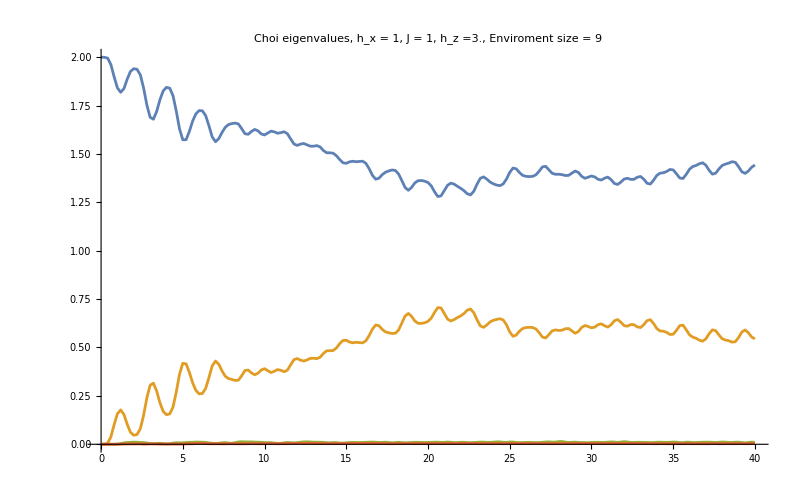

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```

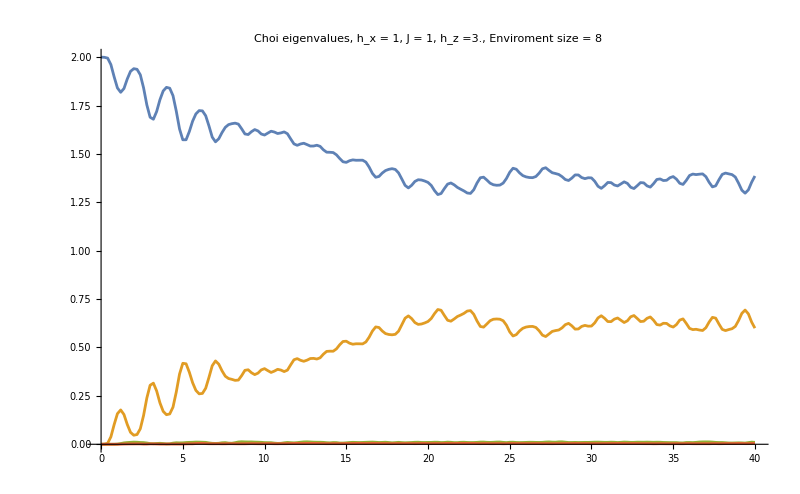

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```

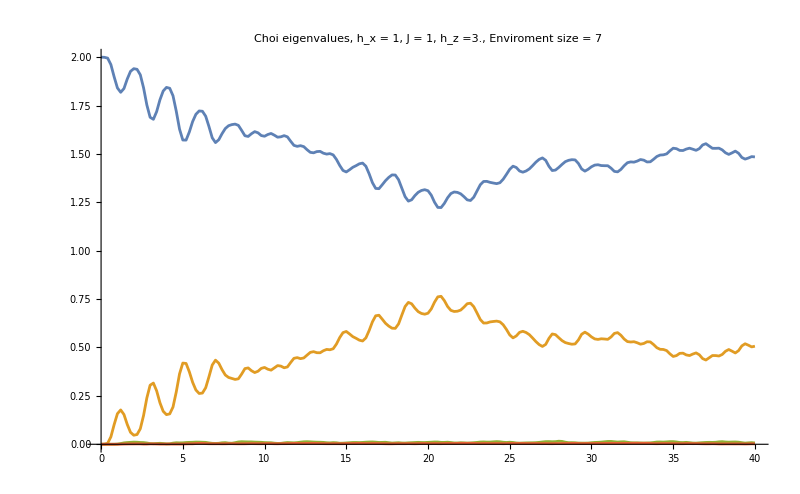

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```

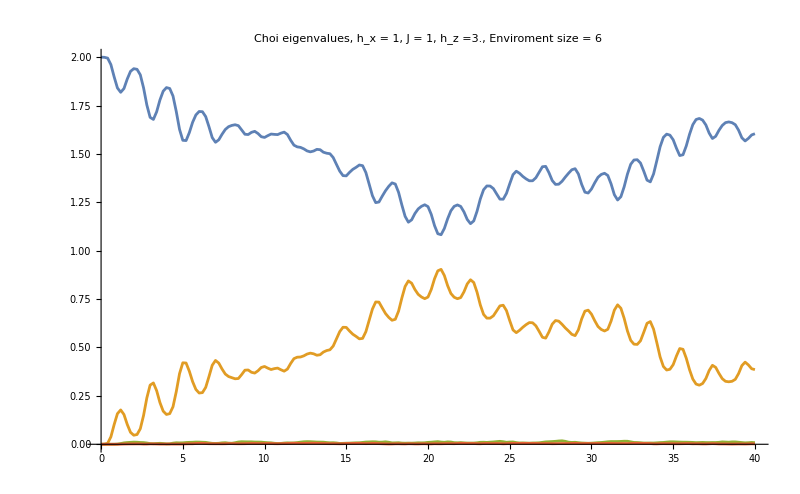

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```

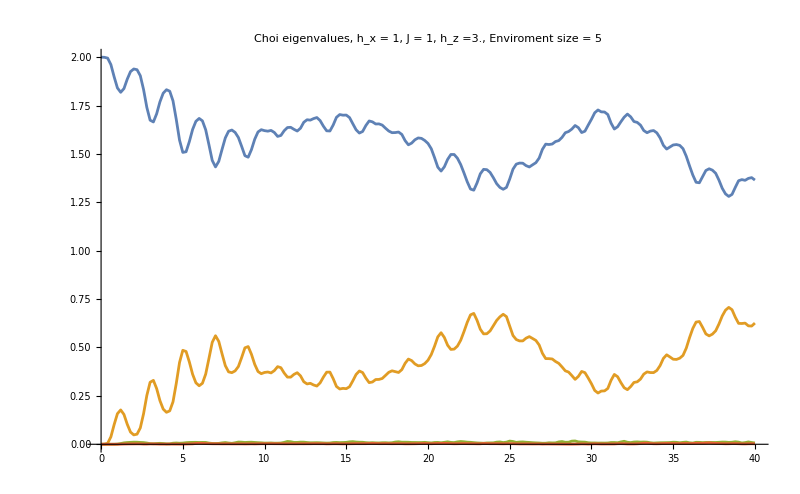

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```

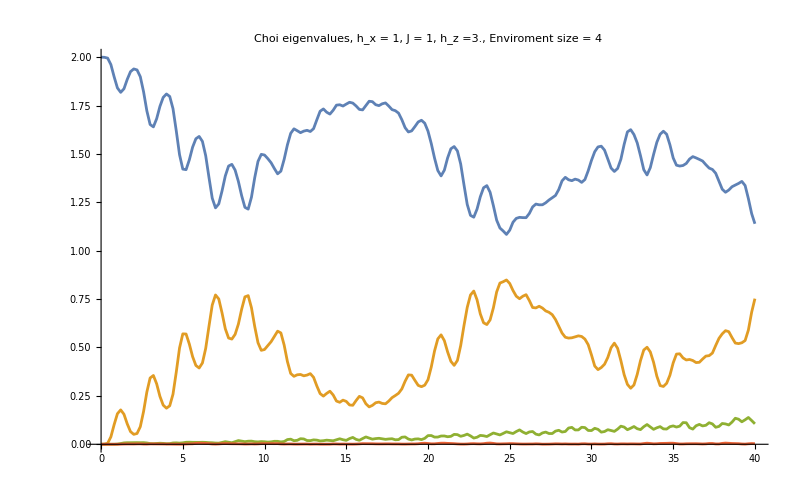

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```

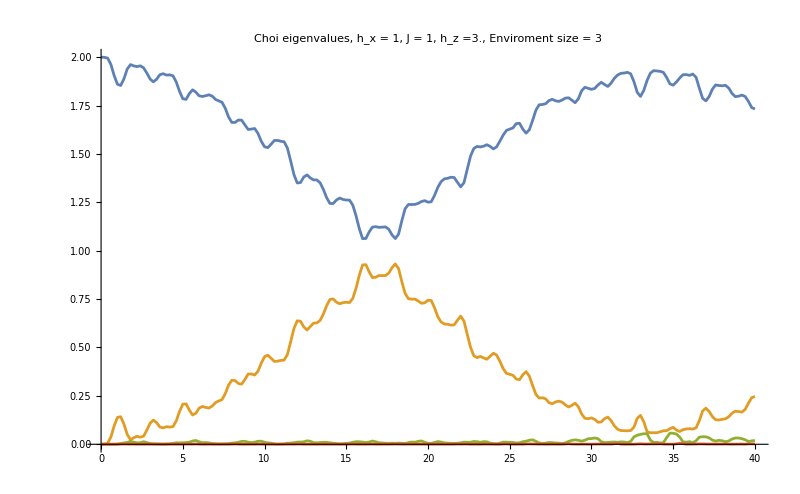

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```

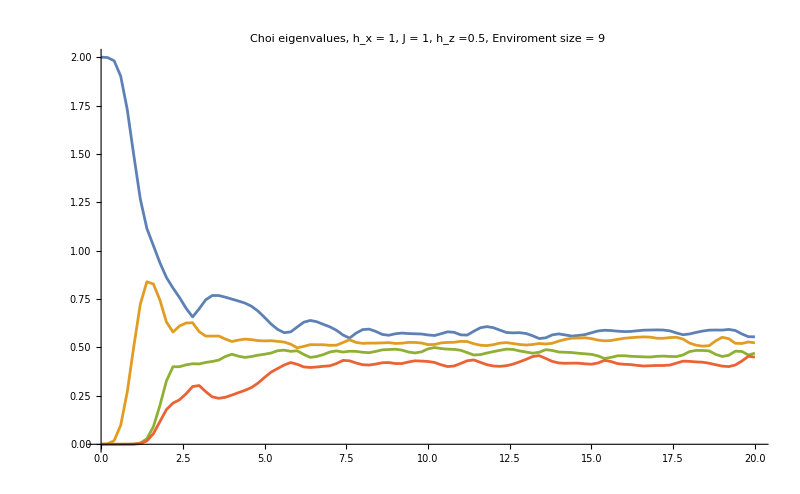

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```

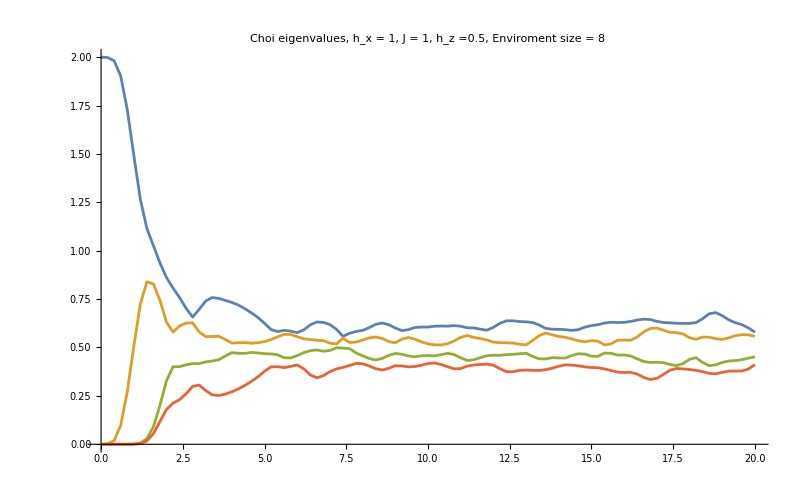

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```

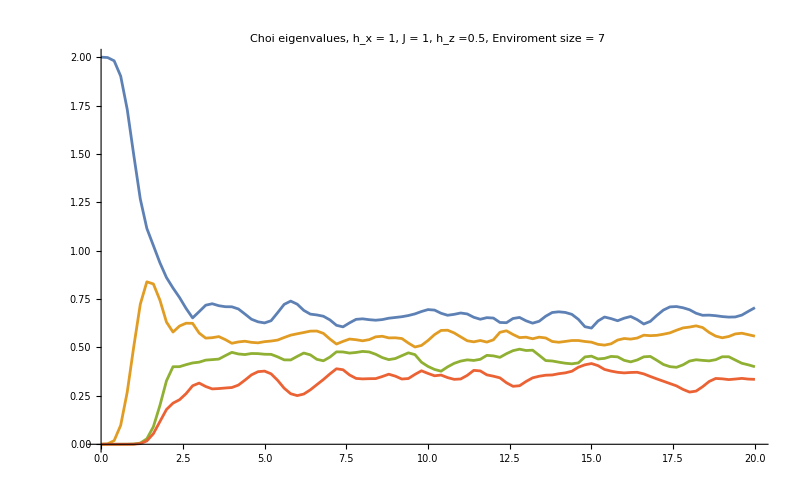

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```

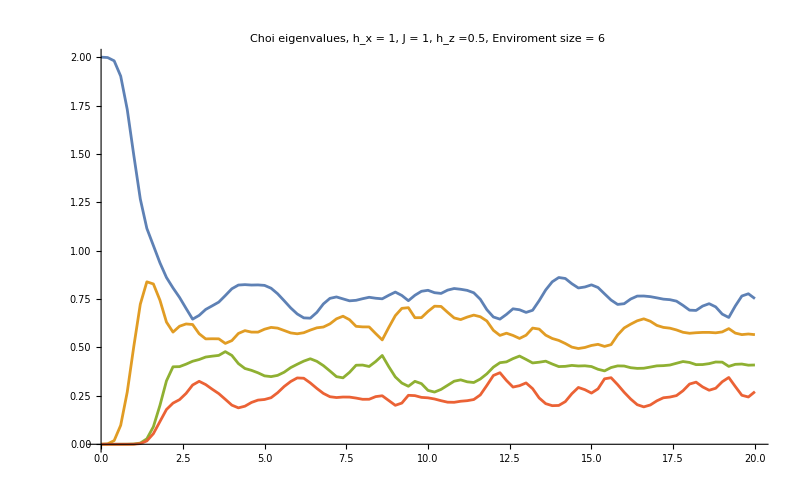

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```

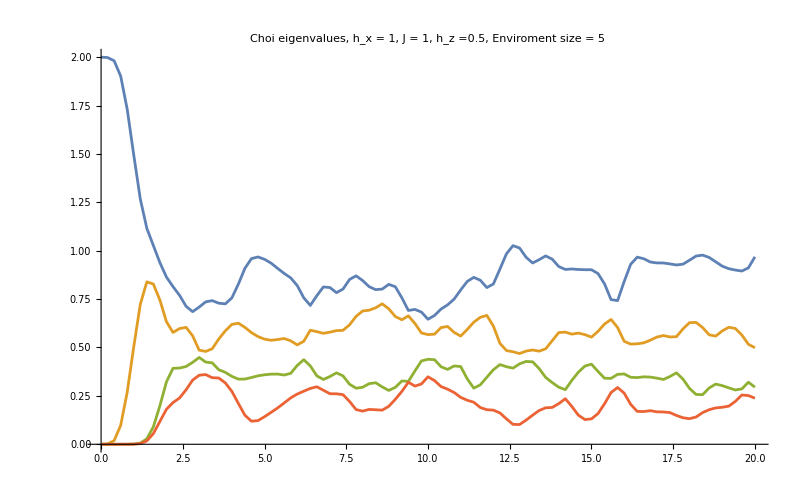

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```

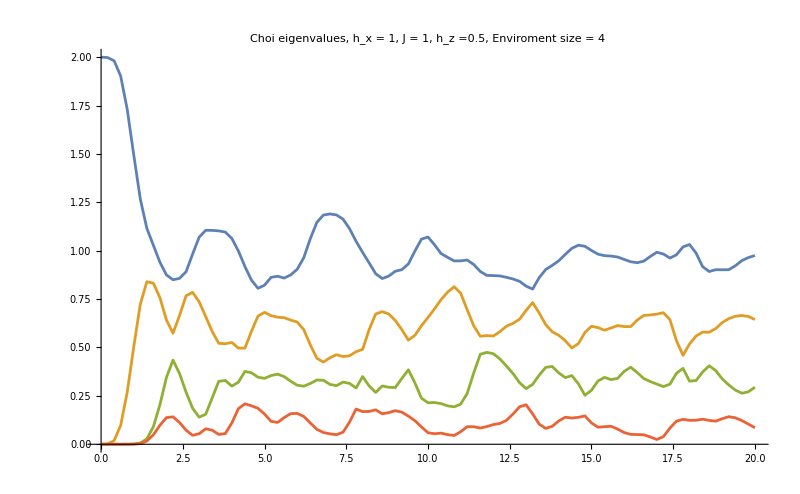

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```

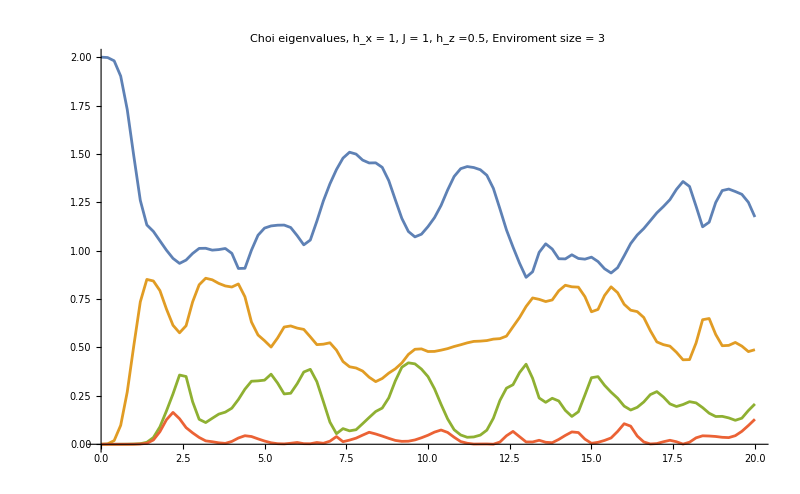

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues, h_x = 1, J = 1, h_z ="<>ToString[hz]<>", Enviroment size = "<>ToString[L],25,Black]]
```